```mathematica
(Total[Table[allGraphs5[k,"colofournull"],{k,alfa1s}]]==0//Simplify//Factor)/.RepGraph["F"]
```

6 -Graphics-656124+6 -Graphics-218724+6 -Graphics-8124+6 -Graphics-2724+6 -Graphics-324+8 -Graphics-1969213+8 -Graphics-1968413+8 -Graphics-97213+8 -Graphics-73813+8 -Graphics-24413+6 -Graphics-264878+6 -Graphics-204398+6 -Graphics-29178+6 -Graphics-3338+6 -Graphics-138+7 -Graphics-219545+7 -Graphics-87845+7 -Graphics-73745+7 -Graphics-66705+7 -Graphics-24605+5 -Graphics-295240==6 -Graphics-1968321+6 -Graphics-72921+6 -Graphics-24321+6 -Graphics-921+6 -Graphics-121+4 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-658816+4 -Graphics-656215+4 -Graphics-243015+4 -Graphics-221416+4 -Graphics-219016+4 -Graphics-81015+4 -Graphics-8416+4 -Graphics-3615+6 -Graphics-219519+6 -Graphics-87579+6 -Graphics-72939+6 -Graphics-2739+6 -Graphics-1099+5 -Graphics-264885+5 -Graphics-204485+5 -Graphics-196965+5 -Graphics-31605+5 -Graphics-10625+3 -Graphics-287640+3 -Graphics-272460+3 -Graphics-227080+3 -Graphics-94900+3 -Graphics-3640

```mathematica
(Total[Table[allGraphs5[k,"colofourrealnull"],{k,alfa1s}]]==0//Simplify//Factor)/.RepGraph["E"]
```

10 -Graphics-590481+-Graphics-132842+-Graphics-131762+-Graphics-44282+-Graphics-43802+-Graphics-1682==-Graphics-575282+-Graphics-544922+-Graphics-454162+2 -Graphics-439081+-Graphics-189802+-Graphics-7282+2 -Graphics-49201+2 -Graphics-147481+2 -Graphics-133401+2 -Graphics-175681

```mathematica
Table[Reduce[Simplify[allGraphs5[k,"colofourrealnull"]==0],n12345],{k,alfa1s}]//TableForm
```

n12345==n1234x5/2+n135x24/2+n13x245/2-n13x24x5/2
n12345==n1245x3/2+n134x25/2+n14x235/2-n14x25x3/2
n12345==n124x35/2+n135x24/2+n1x2345/2-n1x24x35/2
n12345==n1235x4/2+n134x25/2+n13x245/2-n13x25x4/2
n12345==n124x35/2+n1345x2/2+n14x235/2-n14x2x35/2

```mathematica
Simplify[(n1234x5/2+n135x24/2+n13x245/2-n13x24x5/2==n1245x3/2+n134x25/2+n14x235/2-n14x25x3/2)/.RepGraph["E"]]
```

-Graphics-575282+-Graphics-147481+-Graphics-133401+-Graphics-44282==-Graphics-454162+-Graphics-49201+-Graphics-175681+-Graphics-132842

```mathematica
Simplify[(n1234x5/2+n135x24/2+n13x245/2-n13x24x5/2==n124x35/2+n135x24/2+n1x2345/2-n1x24x35/2)/.RepGraph["E"]]
```

-Graphics-575282+-Graphics-133401+-Graphics-1682==-Graphics-439081+-Graphics-7282+-Graphics-132842

```mathematica
Reduce[n1234x5/2+n135x24/2+n13x245/2-n13x24x5/2==n1245x3/2+n134x25/2+n14x235/2-n14x25x3/2,n1234x5]
```

n1234x5==n1245x3+n134x25-n135x24-n13x245+n13x24x5+n14x235-n14x25x3

```mathematica
Reduce[n124x35/2+n135x24/2+n1x2345/2-n1x24x35/2==n1235x4/2+n134x25/2+n13x245/2-n13x25x4/2,n1234x5]
```

n1235x4==n124x35-n134x25+n135x24-n13x245+n13x25x4+n1x2345-n1x24x35

```mathematica
Reduce[n1234x5/2+n135x24/2+n13x245/2-n13x24x5/2-n1245x3/2+n134x25/2+n14x235/2-n14x25x3/2==n124x35/2+n135x24/2+n1x2345/2-n1x24x35/2-n1235x4/2+n134x25/2+n13x245/2-n13x25x4/2,n1234x5]
```

```mathematica
n1234x5==-n1235x4+n1245x3+n124x35+n13x24x5-n13x25x4-n14x235+n14x25x3+n1x2345-n1x24x35/.RepGraph["E"]
```

-Graphics-575282==--Graphics-544922+-Graphics-454162+-Graphics-439081+-Graphics-7282--Graphics-49201+-Graphics-132842--Graphics-131762+-Graphics-44282--Graphics-1682

```mathematica
Table[Reduce[Simplify[allGraphs5[k,"colofournull"]==0],p12345],{k,alfa1s}]/.RepGraph["F"]//TableForm
```

-Graphics-295240==2 -Graphics-1968321-4 -Graphics-656124+2 -Graphics-218724+2 -Graphics-24321-4 -Graphics-8124+2 -Graphics-921-2 -Graphics-1968615-2 -Graphics-1968413+4 -Graphics-658816+4 -Graphics-656215-2 -Graphics-221416-2 -Graphics-219016-2 -Graphics-97213+4 -Graphics-81015-2 -Graphics-73813-2 -Graphics-24413+4 -Graphics-8416-2 -Graphics-3615-2 -Graphics-204398+4 -Graphics-72939-2 -Graphics-29178-2 -Graphics-2739+4 -Graphics-1099-2 -Graphics-138+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845-5 -Graphics-73745-5 -Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625--Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640
-Graphics-295240==2 -Graphics-1968321-4 -Graphics-218724+2 -Graphics-72921+2 -Graphics-8124-4 -Graphics-2724+2 -Graphics-121-2 -Graphics-1969213-2 -Graphics-1968615-2 -Graphics-664216+4 -Graphics-658816-2 -Graphics-656215+4 -Graphics-243015+4 -Graphics-219016-2 -Graphics-97213-2 -Graphics-73813-2 -Graphics-24413-2 -Graphics-8416+4 -Graphics-3615-2 -Graphics-264878+4 -Graphics-87579-2 -Graphics-72939-2 -Graphics-3338+4 -Graphics-2739-2 -Graphics-138+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965-5 -Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605-5 -Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460--Graphics-227080+-Graphics-94900+-Graphics-3640
-Graphics-295240==2 -Graphics-24321-4 -Graphics-8124+2 -Graphics-2724+2 -Graphics-921-4 -Graphics-324+2 -Graphics-121-2 -Graphics-1969213+4 -Graphics-1968615-2 -Graphics-1968413+4 -Graphics-664216-2 -Graphics-658816-2 -Graphics-656215-2 -Graphics-243015-2 -Graphics-221416+4 -Graphics-219016-2 -Graphics-97213+4 -Graphics-81015-2 -Graphics-73813-2 -Graphics-264878+4 -Graphics-219519-2 -Graphics-204398-2 -Graphics-87579+4 -Graphics-72939-2 -Graphics-29178+-Graphics-264885-5 -Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845-5 -Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900--Graphics-3640
-Graphics-295240==2 -Graphics-1968321-4 -Graphics-656124+2 -Graphics-72921+2 -Graphics-24321-4 -Graphics-2724+2 -Graphics-324-2 -Graphics-1969213-2 -Graphics-1968413+4 -Graphics-664216+4 -Graphics-656215-2 -Graphics-243015+4 -Graphics-221416-2 -Graphics-219016-2 -Graphics-81015-2 -Graphics-73813-2 -Graphics-24413-2 -Graphics-8416+4 -Graphics-3615-2 -Graphics-219519+4 -Graphics-87579-2 -Graphics-29178-2 -Graphics-3338+4 -Graphics-1099-2 -Graphics-138+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965-5 -Graphics-87845+-Graphics-73745-5 -Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640--Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640
-Graphics-295240==2 -Graphics-656124-4 -Graphics-218724+2 -Graphics-72921+2 -Graphics-921-4 -Graphics-324+2 -Graphics-121-2 -Graphics-1969213+4 -Graphics-1968615-2 -Graphics-1968413-2 -Graphics-664216-2 -Graphics-658816+4 -Graphics-243015+4 -Graphics-221416-2 -Graphics-97213-2 -Graphics-81015-2 -Graphics-24413+4 -Graphics-8416-2 -Graphics-3615-2 -Graphics-264878+4 -Graphics-219519-2 -Graphics-204398-2 -Graphics-3338+4 -Graphics-2739-2 -Graphics-1099+-Graphics-264885-5 -Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605-5 -Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080--Graphics-94900+-Graphics-3640

```mathematica
Bases
```

<|C→<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,26487,21951,20439,19692,19686,19684,8757,7293,6642,6588,6562,2917,2430,2214,2190,972,810,738,333,273,244,109,84,36,13,28764,27246,26488,22708,21954,20448,19696,9490,8784,7374,6670,3160,2460,1062,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{t1x2x3x4x5,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t123x4x5,t124x3x5,t125x3x4,t12x34x5,t12x35x4,t12x3x45,t134x2x5,t135x2x4,t13x24x5,t13x25x4,t13x2x45,t145x2x3,t14x23x5,t14x25x3,t14x2x35,t15x23x4,t15x24x3,t15x2x34,t1x234x5,t1x235x4,t1x23x45,t1x245x3,t1x24x35,t1x25x34,t1x2x345,t1234x5,t1235x4,t123x45,t1245x3,t124x35,t125x34,t12x345,t1345x2,t134x25,t135x24,t13x245,t145x23,t14x235,t15x234,t1x2345,t12345}|>|>

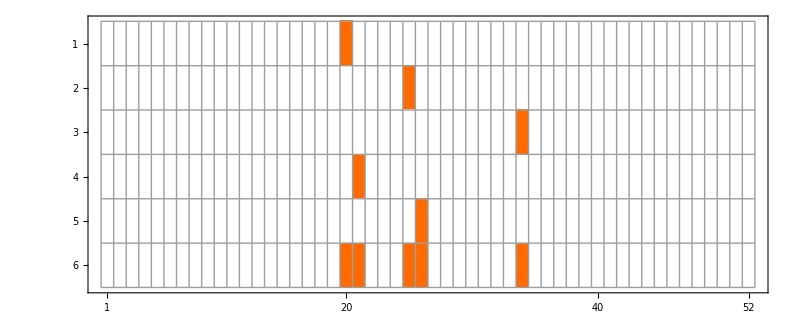
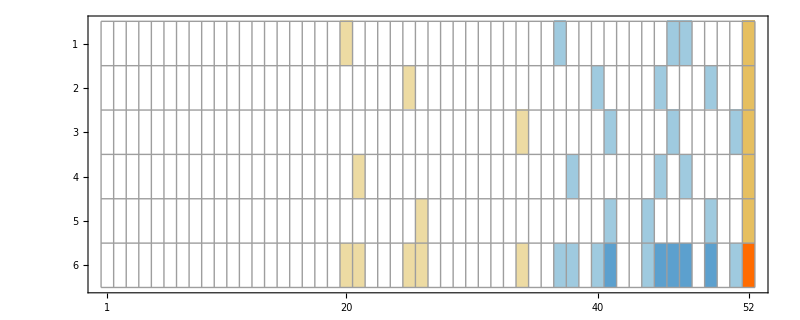
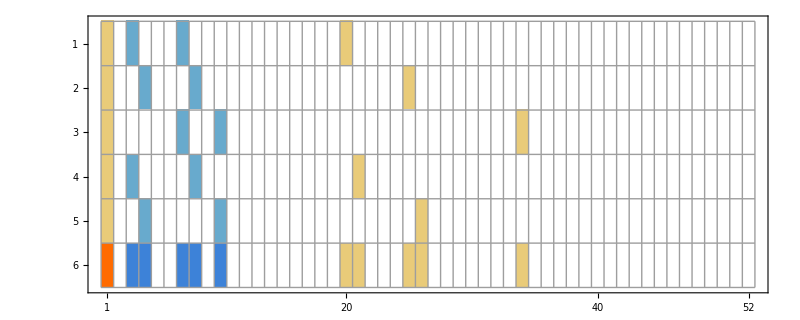
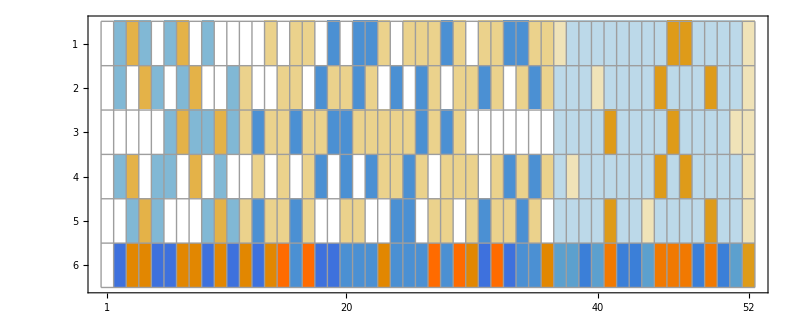
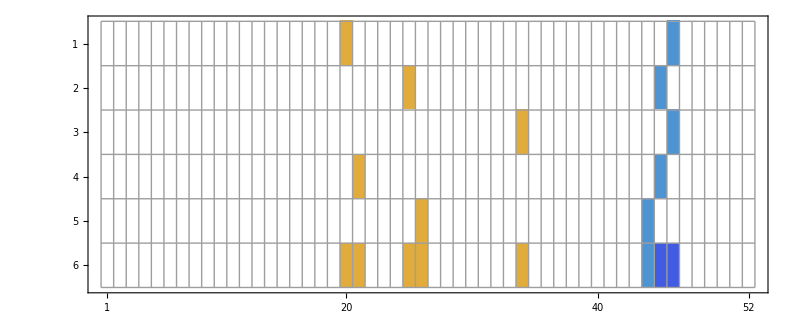
-Graphics-C
-Graphics-E
-Graphics-G
-Graphics-F
-Graphics-T

```mathematica
TableForm[
Table[
Labeled[MatrixPlot[Append[Table[BaseCoeff[k,base],{k,alfa1s}],Total[Table[BaseCoeff[k,base],{k,alfa1s}]]],ImageSize->800,Mesh->All],base],
{base,Keys[Bases]}
]
]
```

```mathematica
Table[Simplify[allGraphs5[k,"colotree"]],{k,alfa1s}]/.RepGraph["T"]//TableForm
```

--Graphics-368980+-Graphics-354340
--Graphics-383080+-Graphics-251680
--Graphics-368980+-Graphics-223180
--Graphics-383080+-Graphics-339160
--Graphics-390141+-Graphics-244141

```mathematica
Table[Simplify[allGraphs5[k,"colofourgenerator"]],{k,alfa1s}]/.RepGraph["G"]//TableForm
```

-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240
-Graphics-273100--Graphics-294970--Graphics-273370+-Graphics-295240
-Graphics-294400--Graphics-295210--Graphics-294430+-Graphics-295240
-Graphics-229360--Graphics-294970--Graphics-229630+-Graphics-295240
-Graphics-273340--Graphics-295210--Graphics-273370+-Graphics-295240

```mathematica
Total[Table[Simplify[allGraphs5[k,"colofourgenerator"]],{k,alfa1s}]]/.RepGraph["G"]//TableForm
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820-2 -Graphics-295210-2 -Graphics-294970-2 -Graphics-294430-2 -Graphics-273370-2 -Graphics-229630+5 -Graphics-295240

```mathematica
Total[Table[Simplify[allGraphs5[k,"colotree"]],{k,alfa1s}]]/.RepGraph["T"]
```

--Graphics-390141-2 -Graphics-368980-2 -Graphics-383080+-Graphics-354340+-Graphics-339160+-Graphics-251680+-Graphics-244141+-Graphics-223180

```mathematica
Total[Table[Simplify[allGraphs5[k,"colotree"]],{k,Take[alfa1s,4]}]]/.RepGraph["T"]
```

-2 -Graphics-368980-2 -Graphics-383080+-Graphics-354340+-Graphics-339160+-Graphics-251680+-Graphics-223180

```mathematica
Total[Table[Simplify[allGraphs5[k,"colotree"]],{k,Take[alfa1s,3]}]]/.RepGraph["T"]
```

-2 -Graphics-368980--Graphics-383080+-Graphics-354340+-Graphics-251680+-Graphics-223180

```mathematica
Total[Table[Simplify[allGraphs5[k,"colotree"]],{k,Take[alfa1s,2]}]]/.RepGraph["T"]
```

--Graphics-368980--Graphics-383080+-Graphics-354340+-Graphics-251680

```mathematica
Fold[And,Table[Simplify[allGraphs5[k,"colotree"]==0],{k,alfa1s}]]/.RepGraph["T"]
```

-Graphics-368980==-Graphics-354340&&-Graphics-383080==-Graphics-251680&&-Graphics-368980==-Graphics-223180&&-Graphics-383080==-Graphics-339160&&-Graphics-390141==-Graphics-244141

```mathematica
Simplify[Fold[And,Table[Simplify[allGraphs5[k,"colotree"]==0],{k,alfa1s}]]]
```

t135x24==t13x24x5&&t134x25==t14x25x3&&t135x24==t1x24x35&&t134x25==t13x25x4&&t1345x2==t14x2x35

```mathematica
Simplify[Fold[And,Table[Simplify[allGraphs5[k,"colofourgenerator"]==0],{k,alfa1s}]]]/.RepGraph["G"]
```

-Graphics-228820+-Graphics-295240==-Graphics-294430+-Graphics-229630&&-Graphics-273100+-Graphics-295240==-Graphics-294970+-Graphics-273370&&-Graphics-294400+-Graphics-295240==-Graphics-295210+-Graphics-294430&&-Graphics-229360+-Graphics-295240==-Graphics-294970+-Graphics-229630&&-Graphics-273340+-Graphics-295240==-Graphics-295210+-Graphics-273370

```mathematica
Simplify[Fold[And,Table[Simplify[allGraphs5[k,"colofournull"]==0],{k,alfa1s}]]]/.RepGraph["F"]
```

4 -Graphics-656124+4 -Graphics-8124+2 -Graphics-1968615+2 -Graphics-1968413+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-3615+2 -Graphics-204398+2 -Graphics-29178+2 -Graphics-2739+2 -Graphics-138+5 -Graphics-73745+5 -Graphics-66705+-Graphics-287640+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-218724+2 -Graphics-24321+2 -Graphics-921+4 -Graphics-658816+4 -Graphics-656215+4 -Graphics-81015+4 -Graphics-8416+4 -Graphics-72939+4 -Graphics-1099+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640&&4 -Graphics-218724+4 -Graphics-2724+2 -Graphics-1969213+2 -Graphics-1968615+2 -Graphics-664216+2 -Graphics-656215+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+2 -Graphics-264878+2 -Graphics-72939+2 -Graphics-3338+2 -Graphics-138+5 -Graphics-87845+5 -Graphics-24605+-Graphics-227080+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-8124+2 -Graphics-121+4 -Graphics-658816+4 -Graphics-243015+4 -Graphics-219016+4 -Graphics-3615+4 -Graphics-87579+4 -Graphics-2739+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-94900+-Graphics-3640&&4 -Graphics-8124+4 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-658816+2 -Graphics-656215+2 -Graphics-243015+2 -Graphics-221416+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-87579+2 -Graphics-29178+5 -Graphics-219545+5 -Graphics-73745+-Graphics-3640+-Graphics-295240==2 -Graphics-24321+2 -Graphics-2724+2 -Graphics-921+2 -Graphics-121+4 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-219016+4 -Graphics-81015+4 -Graphics-219519+4 -Graphics-72939+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900&&4 -Graphics-656124+4 -Graphics-2724+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-243015+2 -Graphics-219016+2 -Graphics-81015+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+2 -Graphics-219519+2 -Graphics-29178+2 -Graphics-3338+2 -Graphics-138+5 -Graphics-87845+5 -Graphics-66705+-Graphics-272460+-Graphics-295240==2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-24321+2 -Graphics-324+4 -Graphics-664216+4 -Graphics-656215+4 -Graphics-221416+4 -Graphics-3615+4 -Graphics-87579+4 -Graphics-1099+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-73745+-Graphics-31605+-Graphics-24605+-Graphics-10625+-Graphics-287640+-Graphics-227080+-Graphics-94900+-Graphics-3640&&4 -Graphics-218724+4 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-664216+2 -Graphics-658816+2 -Graphics-97213+2 -Graphics-81015+2 -Graphics-24413+2 -Graphics-3615+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-3338+2 -Graphics-1099+5 -Graphics-219545+5 -Graphics-24605+-Graphics-94900+-Graphics-295240==2 -Graphics-656124+2 -Graphics-72921+2 -Graphics-921+2 -Graphics-121+4 -Graphics-1968615+4 -Graphics-243015+4 -Graphics-221416+4 -Graphics-8416+4 -Graphics-219519+4 -Graphics-2739+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-3640

```mathematica
Sort[Tally[Flatten[Table[ListofVars[allGraphs5[k,"colofournull"]],{k,alfa1s}]]],#1[[2]]<#2[[2]]&]
```

{{p1x2x35x4,3},{p124x3x5,3},{p1x2x3x45,3},{p1x25x3x4,3},{p1x234x5,3},{p15x2x3x4,3},{p134x2x5,3},{p123x4x5,3},{p1x2x34x5,3},{p1x2x345,3},{p1x24x3x5,3},{p1x245x3,3},{p1x23x4x5,3},{p1x235x4,3},{p14x2x3x5,3},{p145x2x3,3},{p13x2x4x5,3},{p135x2x4,3},{p12x3x4x5,3},{p125x3x4,3},{p14x23x5,4},{p13x24x5,4},{p12x34x5,4},{p1x25x34,4},{p1x24x35,4},{p1x23x45,4},{p15x2x34,4},{p15x24x3,4},{p15x23x4,4},{p14x2x35,4},{p14x25x3,4},{p13x2x45,4},{p13x25x4,4},{p12x3x45,4},{p12x35x4,4},{p1x2345,5},{p15x234,5},{p14x235,5},{p145x23,5},{p13x245,5},{p135x24,5},{p134x25,5},{p1345x2,5},{p12x345,5},{p125x34,5},{p124x35,5},{p1245x3,5},{p123x45,5},{p1235x4,5},{p1234x5,5},{p12345,5}}

```mathematica
Eliminate[Simplify[Fold[And,Table[Simplify[allGraphs5[k,"colofournull"]==0],{k,alfa1s}]]],{p12345,p1234x5,p1235x4,p1245x3,p1345x2}]
```

True

```mathematica
Eliminate[Simplify[Fold[And,Table[Simplify[allGraphs5[k,"colofournull"]==0],{k,alfa1s}]]],{p1234x5,p1235x4,p1245x3,p1345x2}]/.RepGraph["F"]
```

3 -Graphics-1968321-3 -Graphics-656124-3 -Graphics-218724+3 -Graphics-72921+3 -Graphics-8124-6 -Graphics-2724+3 -Graphics-324--Graphics-1969213-4 -Graphics-1968615--Graphics-1968413-4 -Graphics-664216+5 -Graphics-658816+5 -Graphics-656215+5 -Graphics-243015+5 -Graphics-221416-4 -Graphics-219016--Graphics-97213-4 -Graphics-81015--Graphics-73813-4 -Graphics-24413+2 -Graphics-8416+2 -Graphics-3615-3 -Graphics-219519+6 -Graphics-87579-3 -Graphics-72939-3 -Graphics-3338+3 -Graphics-2739+3 -Graphics-1099-3 -Graphics-138+-Graphics-264885+4 -Graphics-219545+-Graphics-204485+-Graphics-196965-5 -Graphics-87845+4 -Graphics-73745-5 -Graphics-66705+-Graphics-31605-5 -Graphics-24605+-Graphics-10625+3 -Graphics-3640==-Graphics-295240